```mathematica
(*PSO 20 particles, 100 iterations*)
data1={0.3310999999999999,0.33109999999999984,0.33109999999999984,0.3311000000000235,0.3311000000003633,0.33110000000772666,0.3311000000000046,0.3311000000050604,0.3311000000003207,0.33110000000000916,0.33110000000001394,0.33110000000000456,0.33110000000376394,0.3311000000159755,0.33110000000032175};
```

```mathematica
{Mean[data1],Median[data2],Median[data3]}
```

{0.3311,0.3311,0.3311}

```mathematica
(*PSO 20 particles, 500 iterations*)
data2 = {0.33109999999999984,0.3310999999999999,0.33109999999999984,0.33109999999999984,0.3310999999999998,0.3310999999999999,0.33109999999999984,0.33109999999999984,0.3310999999999998,0.3310999999999999,0.3311,0.33109999999999984,0.33109999999999984,0.33109999999999984,0.3311000000000085};
```

```mathematica
StandardDeviation[data1]
```

4.47073×10^-12

```mathematica
StandardDeviation[data2]
```

2.2328×10^-15

```mathematica
StandardDeviation[data1](*StdDev for 20np 100nit*)
```

4.47073×10^-12

```mathematica
StandardDeviation[data2](*StdDev for 20np 500nit*)
```

2.60506×10^-15

```mathematica
(*PSO 40 particles, 100 iterations*)data3 = {0.3311000000024352,0.33110000001074713,0.3311000000000046,0.33110000000082634,0.3311000000002402,0.3311000000001075,0.33110000022497593,0.3311000000000255,0.3310999999999999,0.3310999999999999,0.3311};
```

```mathematica
StandardDeviation[data3](*StdDev for 40np 100nit*)
```

6.74743×10^-11

```mathematica
data4=Flatten[Import["~/Desktop/Uni\ shizz\ 4th\ year/CS4525\ Project/Haskell/ghc-eden-7.6.1/testing2.txt","Data"]]

Sort[{0.3310999999999999,0.33109999999999984,0.33109999999999984,0.3311000000000235,0.3311000000003633,0.33110000000772666,0.3311000000000046,0.3311000000050604,0.3311000000003207,0.33110000000000916,0.33110000000001394,0.33110000000000456,0.33110000000376394,0.3311000000159755,0.33110000000032175},Less]
```

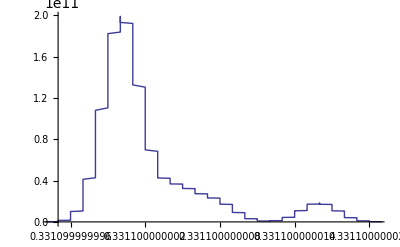

```mathematica
SmoothHistogram[data1,Automatic,"PDF"]
```

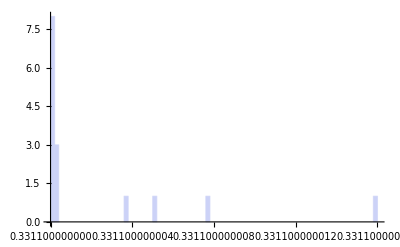

```mathematica
Histogram[data1,100]
```

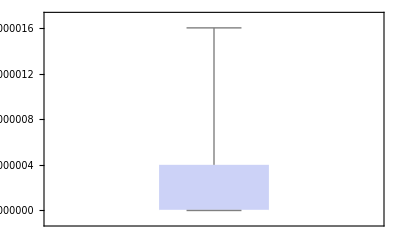

```mathematica
BoxWhiskerChart[data1]
```

```mathematica
(*Following is the data for testPSO.txt which tests constriction factors.*)
```

```mathematica
data21 = {0.9140999999999991,0.9140999999999992,0.9140999999999991,0.9140999999999995,0.9140999999999996,0.9140999999999992,0.9140999999999992,0.9140999999999992,0.9140999999999992,0.9140999999999992,0.914099999999999,0.9140999999999991,0.9140999999999992,0.9140999999999989,0.9140999999999992,0.9140999999999991,0.9140999999999995,0.9140999999999994,0.9140999999999994,0.914099999999999}
StandardDeviation[data1]
```

{0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141}

1.61088×10^-16

```mathematica
data22={0.914099999999999,0.9140999999999989,0.914099999999999,0.9140999999999992,0.914099999999999,0.9140999999999992,0.9140999999999989,0.9140999999999991,0.914099999999999,0.914099999999999,0.9140999999999994,0.914099999999999,0.9140999999999989,0.9140999999999989,0.9140999999999991,0.9140999999999992,0.9140999999999995,0.9140999999999991,0.9140999999999989,0.9140999999999989}
StandardDeviation[data22]
```

{0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141}

1.72748×10^-16

```mathematica
data23={0.9141001344878226,0.9141020842615248,0.9141010076244758,0.9141000114198997,0.9141000103020339,0.9141024297655886,0.9141007738801588,0.9141000259586043,0.9141018344721783,0.9141014994960018,0.9141003050067964,0.9141010556811353,0.9141062103584059,0.9141031410691673,0.914102377844142,0.914124441556149,0.9141000006683239,0.914102199493055,0.9141043312183866,0.9141004708536062}
StandardDeviation[data23]
```

{0.9141,0.914102,0.914101,0.9141,0.9141,0.914102,0.914101,0.9141,0.914102,0.914101,0.9141,0.914101,0.914106,0.914103,0.914102,0.914124,0.9141,0.914102,0.914104,0.9141}

5.36229×10^-6

```mathematica
data24={0.9141411881129956,0.9142005342311976,0.9141141171255334,0.9141867837565565,0.9141239752730616,0.9142431378146977,0.914137262801665,0.9141572395703302,0.9142355194539499,0.9141577443834252,0.9141662114223291,0.9141690348891207,0.9141737318170899,0.9141566270443193,0.9141062723726792,0.9141166773383033,0.9141792857146174,0.9141342099643939,0.9141067710143833,0.9141320715810547}
StandardDeviation[data24]
```

{0.914141,0.914201,0.914114,0.914187,0.914124,0.914243,0.914137,0.914157,0.914236,0.914158,0.914166,0.914169,0.914174,0.914157,0.914106,0.914117,0.914179,0.914134,0.914107,0.914132}

0.0000389374

```mathematica
data25={0.914207596085302,0.91410321295459,0.9141196037619853,0.9142050979079516,0.9141245974709327,0.9141354420720601,0.9141424308495572,0.9141562583836846,0.9141046285841078,0.914105964764435,0.9142182359110826,0.9141383751330914,0.9141581541960425,0.9141123639329142,0.9141030261707,0.9141809343286167,0.9141866887778222,0.9142579749158725,0.9141140927277053,0.9141606396285045}
StandardDeviation[data25]
```

{0.914208,0.914103,0.91412,0.914205,0.914125,0.914135,0.914142,0.914156,0.914105,0.914106,0.914218,0.914138,0.914158,0.914112,0.914103,0.914181,0.914187,0.914258,0.914114,0.914161}

0.0000448388

```mathematica
data26={0.9140999999999992,0.9140999999999995,0.914099999999999,0.9140999999999992,0.914099999999999,0.914099999999999,0.9140999999999991,0.9140999999999987,0.9140999999999995,0.9140999999999988,0.9140999999999991,0.9140999999999991,0.914099999999999,0.9140999999999991,0.9140999999999996,0.9140999999999992,0.9140999999999994,0.9140999999999985,0.9140999999999996,0.9140999999999991}
StandardDeviation[data26]
```

{0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141}

2.81328×10^-16